# Program for Cases Management in Israel

## Curve of Totals

```mathematica
SetDirectory["/Users/zhuohuizhang/Dropbox/israelcases"]
```

/Users/zhuohuizhang/Dropbox/IsraelCases

```mathematica
WebpageContent=Import["israelhealth.htm","Text"];
```

```mathematica
"<tr class=\"zbTRBlue2 zebraPhone\" id=\"TRItem_603e8417-0f76-4b93-884e-f8288d8e6100_3029\"><td class=\"gvDate\" >11.03.2020</td><td class=\"GovXMainTitleContent\"><a href=\"https://www.health.gov.il/NewsAndEvents/SpokemanMesseges/Pages/11032020_13.aspx\" title=\"חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת\" class=\"pagesListLink\" target=\"_blank\"><span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת</span><a></td></tr>"
```

<tr class="zbTRBlue2 zebraPhone" id="TRItem_603e8417-0f76-4b93-884e-f8288d8e6100_3029"><td class="gvDate" >11.03.2020</td><td class="GovXMainTitleContent"><a href="https://www.health.gov.il/NewsAndEvents/SpokemanMesseges/Pages/11032020_13.aspx" title="חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת" class="pagesListLink" target="_blank"><span xmlns:GxMSSettings="urn:GxMSSettings" xmlns:ddwrt="http://schemas.microsoft.com/WebParts/v2/DataView/runtime">חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת</span><a></td></tr>

```mathematica
hexstring={CharacterRange["0","9"],CharacterRange["a","f"]}..;
hebrewname=Except["<"]..;
purenumber=CharacterRange["0","9"]..;
```

```mathematica
PatternForDate="<td class=\"gvDate\" >"~~purenumber~~"."~~purenumber~~"."~~purenumber~~"</td>";
PatternForContent="<span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">"~~hebrewname~~"</span>";
```

```mathematica
ListOfNewsTitles={StringCases[#[[1]],purenumber~~"."~~purenumber~~"."~~purenumber][[1]],StringDelete[#[[2]],{"<span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">","</span>"}]}&/@Partition[StringCases[WebpageContent,{PatternForDate,PatternForContent}],2];
```

```mathematica
GetNumber[str_]:=StringCases[#,purenumber]&/@(Join[StringCases[str,{"מספר "~~purenumber~~"-"~~purenumber,"מס' "~~purenumber~~"-"~~purenumber,"חולה "~~purenumber~~"-"~~purenumber}],StringCases[str,{"מספר "~~purenumber,"מס' "~~purenumber,"חולה "~~purenumber}]])//Flatten//DeleteDuplicates;
CalendarPatients={#[[1]],GetNumber[#[[2]]]}&/@ListOfNewsTitles;
```

```mathematica
DateListCorona=DateString[#,{"Day",".","Month",".","Year"}]&/@DateRange[DateObject[{2020,2,28}],Today];
PatientListGross=Association[Table[date->(ToExpression/@( Select[CalendarPatients,#[[1]]==DateString[date,{"Day",".","Month",".","Year"}]&] ⟦All,2⟧//Flatten//DeleteDuplicates//Sort)),{date,DateRange[DateObject[{2020,2,28}],Today]}]];
PatientListRefined=Module[{historicalpatients,k,refinedlist},
historicalpatients={2,3,4,5};
refinedlist={};
For[k=DateObject[{2020,2,28},"Day","Gregorian",2.],k≤ Today,k=k+Quantity[1,"Days"],
refinedlist=Append[refinedlist,{k,Complement[PatientListGross[k],historicalpatients],Max[Union[historicalpatients,PatientListGross[k]]],Length[Complement[PatientListGross[k],historicalpatients]]}];
historicalpatients=Union[historicalpatients,PatientListGross[k]];
];
refinedlist
]
```

{{Day: Fri 28 Feb 2020,{6,7},7,2},{Day: Sat 29 Feb 2020,{},7,0},{Day: Sun 1 Mar 2020,{8,9,10},10,3},{Day: Mon 2 Mar 2020,{11,12},12,2},{Day: Tue 3 Mar 2020,{},12,0},{Day: Wed 4 Mar 2020,{13,14,15},15,3},{Day: Thu 5 Mar 2020,{16,17},17,2},{Day: Fri 6 Mar 2020,{19,20,21},21,3},{Day: Sat 7 Mar 2020,{18,22,23,24,25},25,5},{Day: Sun 8 Mar 2020,{26,27,28,29},29,4},{Day: Mon 9 Mar 2020,{30,31,32,33,34,35,36,37,39,40,42,43,44,45,46,49,50},50,17},{Day: Tue 10 Mar 2020,{47,48,51,52,53,56,57,58,59,60,61,62,63,65,66,67,70},70,17},{Day: Wed 11 Mar 2020,{64,71,72,73,74,75,76,77,78,79},79,10}}

```mathematica
PatientListNumber=PatientListRefined⟦All,{1,3}⟧;
PatientListIncrement=PatientListRefined⟦All,{1,4}⟧;
```

```mathematica
Export["images/totalcases.svg",{PatientListNumber,PatientListIncrement}//DateListPlot[#,PlotLabel->"Reported Cases in Israel",PlotLegends->{"Total Confirmed","Increment"}]&,"SVG"]
```

images/totalcases.svg

## The Program

## List of Countries

```mathematica
CountryList={Entity["Country","Afghanistan"],Entity["Country","AlandIslands"],Entity["Country","Albania"],Entity["Country","Algeria"],Entity["Country","AmericanSamoa"],Entity["Country","Andorra"],Entity["Country","Angola"],Entity["Country","Anguilla"],Entity["Country","AntiguaBarbuda"],Entity["Country","Argentina"],Entity["Country","Armenia"],Entity["Country","Aruba"],Entity["Country","Australia"],Entity["Country","Austria"],Entity["Country","Azerbaijan"],Entity["Country","Bahamas"],Entity["Country","Bahrain"],Entity["Country","Bangladesh"],Entity["Country","Barbados"],Entity["Country","Belarus"],Entity["Country","Belgium"],Entity["Country","Belize"],Entity["Country","Benin"],Entity["Country","Bermuda"],Entity["Country","Bhutan"],Entity["Country","Bolivia"],Entity["Country","BonaireSintEustatiusAndSaba"],Entity["Country","BosniaHerzegovina"],Entity["Country","Botswana"],Entity["Country","BouvetIsland"],Entity["Country","Brazil"],Entity["Country","BritishIndianOceanTerritory"],Entity["Country","BritishVirginIslands"],Entity["Country","Brunei"],Entity["Country","Bulgaria"],Entity["Country","BurkinaFaso"],Entity["Country","Burundi"],Entity["Country","Cambodia"],Entity["Country","Cameroon"],Entity["Country","Canada"],Entity["Country","CapeVerde"],Entity["Country","CaymanIslands"],Entity["Country","CentralAfricanRepublic"],Entity["Country","Chad"],Entity["Country","Chile"],Entity["Country","China"],Entity["Country","ChristmasIsland"],Entity["Country","CocosKeelingIslands"],Entity["Country","Colombia"],Entity["Country","Comoros"],Entity["Country","CookIslands"],Entity["Country","CostaRica"],Entity["Country","Croatia"],Entity["Country","Cuba"],Entity["Country","Curacao"],Entity["Country","Cyprus"],Entity["Country","CzechRepublic"],Entity["Country","DemocraticRepublicCongo"],Entity["Country","Denmark"],Entity["Country","Djibouti"],Entity["Country","Dominica"],Entity["Country","DominicanRepublic"],Entity["Country","EastTimor"],Entity["Country","Ecuador"],Entity["Country","Egypt"],Entity["Country","ElSalvador"],Entity["Country","EquatorialGuinea"],Entity["Country","Eritrea"],Entity["Country","Estonia"],Entity["Country","Ethiopia"],Entity["Country","FalklandIslands"],Entity["Country","FaroeIslands"],Entity["Country","Fiji"],Entity["Country","Finland"],Entity["Country","France"],Entity["Country","FrenchGuiana"],Entity["Country","FrenchPolynesia"],Entity["Country","FrenchSouthernAndAntarcticLands"],Entity["Country","Gabon"],Entity["Country","Gambia"],Entity["Country","GazaStrip"],Entity["Country","Georgia"],Entity["Country","Germany"],Entity["Country","Ghana"],Entity["Country","Gibraltar"],Entity["Country","Greece"],Entity["Country","Greenland"],Entity["Country","Grenada"],Entity["Country","Guadeloupe"],Entity["Country","Guam"],Entity["Country","Guatemala"],Entity["Country","Guernsey"],Entity["Country","Guinea"],Entity["Country","GuineaBissau"],Entity["Country","Guyana"],Entity["Country","Haiti"],Entity["Country","Honduras"],Entity["Country","HongKong"],Entity["Country","Hungary"],Entity["Country","Iceland"],Entity["Country","India"],Entity["Country","Indonesia"],Entity["Country","Iran"],Entity["Country","Iraq"],Entity["Country","Ireland"],Entity["Country","IsleOfMan"],Entity["Country","Israel"],Entity["Country","Italy"],Entity["Country","IvoryCoast"],Entity["Country","Jamaica"],Entity["Country","Japan"],Entity["Country","Jersey"],Entity["Country","Jordan"],Entity["Country","Kazakhstan"],Entity["Country","Kenya"],Entity["Country","Kiribati"],Entity["Country","Kosovo"],Entity["Country","Kuwait"],Entity["Country","Kyrgyzstan"],Entity["Country","Laos"],Entity["Country","Latvia"],Entity["Country","Lebanon"],Entity["Country","Lesotho"],Entity["Country","Liberia"],Entity["Country","Libya"],Entity["Country","Liechtenstein"],Entity["Country","Lithuania"],Entity["Country","Luxembourg"],Entity["Country","Macau"],Entity["Country","Macedonia"],Entity["Country","Madagascar"],Entity["Country","Malawi"],Entity["Country","Malaysia"],Entity["Country","Maldives"],Entity["Country","Mali"],Entity["Country","Malta"],Entity["Country","MarshallIslands"],Entity["Country","Martinique"],Entity["Country","Mauritania"],Entity["Country","Mauritius"],Entity["Country","Mayotte"],Entity["Country","Mexico"],Entity["Country","Micronesia"],Entity["Country","Moldova"],Entity["Country","Monaco"],Entity["Country","Mongolia"],Entity["Country","Montenegro"],Entity["Country","Montserrat"],Entity["Country","Morocco"],Entity["Country","Mozambique"],Entity["Country","Myanmar"],Entity["Country","Namibia"],Entity["Country","Nauru"],Entity["Country","Nepal"],Entity["Country","Netherlands"],Entity["Country","NewCaledonia"],Entity["Country","NewZealand"],Entity["Country","Nicaragua"],Entity["Country","Niger"],Entity["Country","Nigeria"],Entity["Country","Niue"],Entity["Country","NorfolkIsland"],Entity["Country","NorthernMarianaIslands"],Entity["Country","NorthKorea"],Entity["Country","Norway"],Entity["Country","Oman"],Entity["Country","Pakistan"],Entity["Country","Palau"],Entity["Country","Panama"],Entity["Country","PapuaNewGuinea"],Entity["Country","Paraguay"],Entity["Country","Peru"],Entity["Country","Philippines"],Entity["Country","PitcairnIslands"],Entity["Country","Poland"],Entity["Country","Portugal"],Entity["Country","PuertoRico"],Entity["Country","Qatar"],Entity["Country","RepublicCongo"],Entity["Country","Reunion"],Entity["Country","Romania"],Entity["Country","Russia"],Entity["Country","Rwanda"],Entity["Country","SaintBarthelemy"],Entity["Country","SaintHelena"],Entity["Country","SaintKittsNevis"],Entity["Country","SaintLucia"],Entity["Country","SaintMartin"],Entity["Country","SaintPierreMiquelon"],Entity["Country","SaintVincentGrenadines"],Entity["Country","Samoa"],Entity["Country","SanMarino"],Entity["Country","SaoTomePrincipe"],Entity["Country","SaudiArabia"],Entity["Country","Senegal"],Entity["Country","Serbia"],Entity["Country","Seychelles"],Entity["Country","SierraLeone"],Entity["Country","Singapore"],Entity["Country","SintMaarten"],Entity["Country","Slovakia"],Entity["Country","Slovenia"],Entity["Country","SolomonIslands"],Entity["Country","Somalia"],Entity["Country","SouthAfrica"],Entity["Country","SouthGeorgiaAndTheSouthSandwichIslands"],Entity["Country","SouthKorea"],Entity["Country","SouthSudan"],Entity["Country","Spain"],Entity["Country","SriLanka"],Entity["Country","Sudan"],Entity["Country","Suriname"],Entity["Country","Svalbard"],Entity["Country","Swaziland"],Entity["Country","Sweden"],Entity["Country","Switzerland"],Entity["Country","Syria"],Entity["Country","Taiwan"],Entity["Country","Tajikistan"],Entity["Country","Tanzania"],Entity["Country","Thailand"],Entity["Country","Togo"],Entity["Country","Tokelau"],Entity["Country","Tonga"],Entity["Country","TrinidadTobago"],Entity["Country","Tunisia"],Entity["Country","Turkey"],Entity["Country","Turkmenistan"],Entity["Country","TurksCaicosIslands"],Entity["Country","Tuvalu"],Entity["Country","Uganda"],Entity["Country","Ukraine"],Entity["Country","UnitedArabEmirates"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","UnitedStatesMinorOutlyingIslands"],Entity["Country","UnitedStatesVirginIslands"],Entity["Country","Uruguay"],Entity["Country","Uzbekistan"],Entity["Country","Vanuatu"],Entity["Country","VaticanCity"],Entity["Country","Venezuela"],Entity["Country","Vietnam"],Entity["Country","WallisFutuna"],Entity["Country","WestBank"],Entity["Country","WesternSahara"],Entity["Country","Yemen"],Entity["Country","Zambia"],Entity["Country","Zimbabwe"]};
```

## Specification of City Names

```mathematica
CityToWolframDataWestBank=Association[((#⟦2,1⟧->#)&/@{Entity["City",{"AbuDis","Jerusalem","WestBank"}],Entity["City",{"Abud","RamallahAndAlBireh","WestBank"}],Entity["City",{"Abwein","RamallahAndAlBireh","WestBank"}],Entity["City",{"AdDuhaysah","Bethlehem","WestBank"}],Entity["City",{"Ajjah","Jenin","WestBank"}],Entity["City",{"AlAmarri","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlAraqah","Jenin","WestBank"}],Entity["City",{"AlArrub","Hebron","WestBank"}],Entity["City",{"AlAwja","Jericho","WestBank"}],Entity["City",{"AlAyzariyah","Jerusalem","WestBank"}],Entity["City",{"AlBirah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlFandaqumiyah","Jenin","WestBank"}],Entity["City",{"AlFarah","Tubas","WestBank"}],Entity["City",{"AlFawwar","Hebron","WestBank"}],Entity["City",{"AlfeMenashe","JudeaAndSamaria","Israel"}],Entity["City",{"AlHadr","Bethlehem","WestBank"}],Entity["City",{"AlJalazun","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlJib","Jerusalem","WestBank"}],Entity["City",{"AlJiftlik","Jericho","WestBank"}],Entity["City",{"AlJudaydah","Jenin","WestBank"}],Entity["City",{"AlJudayrah","Jerusalem","WestBank"}],Entity["City",{"AlKarmil","Hebron","WestBank"}],Entity["City",{"AllonShevut","JudeaAndSamaria","Israel"}],Entity["City",{"AlLubbanAsSarqiyah","Nablus","WestBank"}],Entity["City",{"AlMazraahAsSarqiyah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlMugayyir","Jenin","WestBank"}],Entity["City",{"AlMugayyir","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlQubaybah","Jerusalem","WestBank"}],Entity["City",{"AlUbaydiyah","Bethlehem","WestBank"}],Entity["City",{"AlYamun","Jenin","WestBank"}],Entity["City",{"AlZaitounah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Anabta","Tulkarm","WestBank"}],Entity["City",{"Anata","Jerusalem","WestBank"}],Entity["City",{"Anin","Jenin","WestBank"}],Entity["City",{"Anzah","Jenin","WestBank"}],Entity["City",{"AqbahJabbar","Jericho","WestBank"}],Entity["City",{"Aqqaba","Tubas","WestBank"}],Entity["City",{"Aqraba","Nablus","WestBank"}],Entity["City",{"Ariel","JudeaAndSamaria","Israel"}],Entity["City",{"Ariha","Jericho","WestBank"}],Entity["City",{"Arrabah","Jenin","WestBank"}],Entity["City",{"ArRam","Jerusalem","WestBank"}],Entity["City",{"Arranah","Jenin","WestBank"}],Entity["City",{"ArRihiyah","Hebron","WestBank"}],Entity["City",{"ArTas","Bethlehem","WestBank"}],Entity["City",{"Arurah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AsirahAlQibliyah","Nablus","WestBank"}],Entity["City",{"AsirahAsSamaliyah","Nablus","WestBank"}],Entity["City",{"Askar","Nablus","WestBank"}],Entity["City",{"AsSamu","Hebron","WestBank"}],Entity["City",{"AsSawiyah","Nablus","WestBank"}],Entity["City",{"AsSuyuh","Hebron","WestBank"}],Entity["City",{"ATarah","RamallahAndAlBireh","WestBank"}],Entity["City",{"ATTaybah","Jenin","WestBank"}],Entity["City",{"ATTaybah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Attil","Tulkarm","WestBank"}],Entity["City",{"Awarta","Nablus","WestBank"}],Entity["City",{"Aydah","Bethlehem","WestBank"}],Entity["City",{"Aynabus","Nablus","WestBank"}],Entity["City",{"AynYabrud","RamallahAndAlBireh","WestBank"}],Entity["City",{"AzmuT","Nablus","WestBank"}],Entity["City",{"AzZababidah","Jenin","WestBank"}],Entity["City",{"AzZahiriyah","Hebron","WestBank"}],Entity["City",{"AzZawiyah","Salfit","WestBank"}],Entity["City",{"Azzun","Qalqilya","WestBank"}],Entity["City",{"BalataAlBalad","Nablus","WestBank"}],Entity["City",{"BalaTah","Nablus","WestBank"}],Entity["City",{"Bala","Tulkarm","WestBank"}],Entity["City",{"BaniNaim","Hebron","WestBank"}],Entity["City",{"BaqahAsSarqiyah","Tulkarm","WestBank"}],Entity["City",{"BarTaahAsSarqiyah","Jenin","WestBank"}],Entity["City",{"Battir","Bethlehem","WestBank"}],Entity["City",{"Bayta","Nablus","WestBank"}],Entity["City",{"BaytAwwa","Hebron","WestBank"}],Entity["City",{"BaytDajan","Nablus","WestBank"}],Entity["City",{"BaytFajjar","Bethlehem","WestBank"}],Entity["City",{"BaytFurik","Nablus","WestBank"}],Entity["City",{"BaytIba","Nablus","WestBank"}],Entity["City",{"Baytillu","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytImrin","Nablus","WestBank"}],Entity["City",{"BaytJala","Bethlehem","WestBank"}],Entity["City",{"BaytKahil","Hebron","WestBank"}],Entity["City",{"BaytLahm","Bethlehem","WestBank"}],Entity["City",{"BaytLid","Tulkarm","WestBank"}],Entity["City",{"BaytLiqya","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytSahur","Bethlehem","WestBank"}],Entity["City",{"BaytSira","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytSurik","Jerusalem","WestBank"}],Entity["City",{"BaytUla","Hebron","WestBank"}],Entity["City",{"BaytUmmar","Hebron","WestBank"}],Entity["City",{"Baytuniya","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytUrAtTahta","RamallahAndAlBireh","WestBank"}],Entity["City",{"BetarIllit","JudeaAndSamaria","Israel"}],Entity["City",{"BetArye","JudeaAndSamaria","Israel"}],Entity["City",{"BetEl","JudeaAndSamaria","Israel"}],Entity["City",{"Biddu","Jerusalem","WestBank"}],Entity["City",{"Biddya","Salfit","WestBank"}],Entity["City",{"BirNabala","Jerusalem","WestBank"}],Entity["City",{"Birqin","Jenin","WestBank"}],Entity["City",{"BirZayt","RamallahAndAlBireh","WestBank"}],Entity["City",{"Bitin","RamallahAndAlBireh","WestBank"}],Entity["City",{"Bizzariya","Nablus","WestBank"}],Entity["City",{"Bruqin","Salfit","WestBank"}],Entity["City",{"Burin","Nablus","WestBank"}],Entity["City",{"Burqah","Nablus","WestBank"}],Entity["City",{"Burqah","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAbuDaif","Jenin","WestBank"}],Entity["City",{"DayrAbuMasal","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAlGusun","Tulkarm","WestBank"}],Entity["City",{"DayrAlHaTab","Nablus","WestBank"}],Entity["City",{"DayrAmmar","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAsSaraf","Nablus","WestBank"}],Entity["City",{"DayrAsSudan","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrBalluT","Salfit","WestBank"}],Entity["City",{"DayrDibwan","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrIstiya","Salfit","WestBank"}],Entity["City",{"DayrJarir","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrSamit","Hebron","WestBank"}],Entity["City",{"Dhinnabah","Tulkarm","WestBank"}],Entity["City",{"Duma","Nablus","WestBank"}],Entity["City",{"DuraAlQar","RamallahAndAlBireh","WestBank"}],Entity["City",{"Dura","Hebron","WestBank"}],Entity["City",{"Efrata","JudeaAndSamaria","Israel"}],Entity["City",{"EinQiniyye","JudeaAndSamaria","Israel"}],Entity["City",{"Eli","JudeaAndSamaria","Israel"}],Entity["City",{"Elqana","JudeaAndSamaria","Israel"}],Entity["City",{"Fahmah","Jenin","WestBank"}],Entity["City",{"Faqquah","Jenin","WestBank"}],Entity["City",{"Farun","Tulkarm","WestBank"}],Entity["City",{"GevaBinyamin",Missing["NotAvailable"],"Israel"}],Entity["City",{"GivatZeev","JudeaAndSamaria","Israel"}],Entity["City",{"Hablah","Qalqilya","WestBank"}],Entity["City",{"Hajjah","Qalqilya","WestBank"}],Entity["City",{"Halhul","Hebron","WestBank"}],Entity["City",{"HarAdar","JudeaAndSamaria","Israel"}],Entity["City",{"Haras","Hebron","WestBank"}],Entity["City",{"HarbataAlMisbah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Haris","Salfit","WestBank"}],Entity["City",{"Hashmonaim",Missing["NotAvailable"],"Israel"}],Entity["City",{"Hebron","Hebron","WestBank"}],Entity["City",{"HirbatAbuFalah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Hizma","Jerusalem","WestBank"}],Entity["City",{"Hursa","Hebron","WestBank"}],Entity["City",{"Husan","Bethlehem","WestBank"}],Entity["City",{"Huwwara","Nablus","WestBank"}],Entity["City",{"Idhna","Hebron","WestBank"}],Entity["City",{"Iktaba","Tulkarm","WestBank"}],Entity["City",{"Illar","Tulkarm","WestBank"}],Entity["City",{"Immanuel","JudeaAndSamaria","Israel"}],Entity["City",{"Immatin","Qalqilya","WestBank"}],Entity["City",{"Jaba","Jenin","WestBank"}],Entity["City",{"Jaba","Jerusalem","WestBank"}],Entity["City",{"Jalbun","Jenin","WestBank"}],Entity["City",{"Jammain","Nablus","WestBank"}],Entity["City",{"Janin","Jenin","WestBank"}],Entity["City",{"Jayyus","Qalqilya","WestBank"}],Entity["City",{"JinsafuT","Qalqilya","WestBank"}],Entity["City",{"Jit","Qalqilya","WestBank"}],Entity["City",{"KafrAdDik","Salfit","WestBank"}],Entity["City",{"KafrAlLabad","Tulkarm","WestBank"}],Entity["City",{"KafrAqab","Jerusalem","WestBank"}],Entity["City",{"KafrDan","Jenin","WestBank"}],Entity["City",{"KafrJammal","Tulkarm","WestBank"}],Entity["City",{"KafrMalik","RamallahAndAlBireh","WestBank"}],Entity["City",{"KafrNimah","RamallahAndAlBireh","WestBank"}],Entity["City",{"KafrQaddum","Qalqilya","WestBank"}],Entity["City",{"KafrQallil","Nablus","WestBank"}],Entity["City",{"KafrRai","Jenin","WestBank"}],Entity["City",{"KafrTult","Qalqilya","WestBank"}],Entity["City",{"Kawbar","RamallahAndAlBireh","WestBank"}],Entity["City",{"KefarAdummim","JudeaAndSamaria","Israel"}],Entity["City",{"KiflHaris","Salfit","WestBank"}],Entity["City",{"KokhavYaaqov","JudeaAndSamaria","Israel"}],Entity["City",{"Kufayrit","Jenin","WestBank"}],Entity["City",{"Lappid","Hamerkaz","Israel"}],Entity["City",{"MaaleAdummim","JudeaAndSamaria","Israel"}],Entity["City",{"MajdalBaniFadil","Nablus","WestBank"}],Entity["City",{"Mardah","Salfit","WestBank"}],Entity["City",{"Maytalun","Jenin","WestBank"}],Entity["City",{"MazariAnNubari","RamallahAndAlBireh","WestBank"}],Entity["City",{"Misliyah","Jenin","WestBank"}],Entity["City",{"ModiinIllit",Missing["NotAvailable"],"Israel"}],Entity["City",{"ModiinMakkabimReut","Hamerkaz","Israel"}],Entity["City",{"MuhayyamDayrAmmar","RamallahAndAlBireh","WestBank"}],Entity["City",{"MuhayyamJanin","Jenin","WestBank"}],Entity["City",{"MuhayyamQalandiya","Jerusalem","WestBank"}],Entity["City",{"MuhayyamTulkarm","Tulkarm","WestBank"}],Entity["City",{"Nablus","Nablus","WestBank"}],Entity["City",{"Nahhalin","Bethlehem","WestBank"}],Entity["City",{"NazlatIsa","Tulkarm","WestBank"}],Entity["City",{"Nilin","RamallahAndAlBireh","WestBank"}],Entity["City",{"Nuba","Hebron","WestBank"}],Entity["City",{"NurSams","Tulkarm","WestBank"}],Entity["City",{"Ofra","JudeaAndSamaria","Israel"}],Entity["City",{"Qabalan","Nablus","WestBank"}],Entity["City",{"QabaTiyah","Jenin","WestBank"}],Entity["City",{"Qaffin","Tulkarm","WestBank"}],Entity["City",{"Qalqilyah","Qalqilya","WestBank"}],Entity["City",{"QarawatBaniHassan","Salfit","WestBank"}],Entity["City",{"QarawatBaniZayd","RamallahAndAlBireh","WestBank"}],Entity["City",{"QarneShomeron","JudeaAndSamaria","Israel"}],Entity["City",{"Qaryut","Nablus","WestBank"}],Entity["City",{"QaTannah","Jerusalem","WestBank"}],Entity["City",{"Qedummim","JudeaAndSamaria","Israel"}],Entity["City",{"Qibya","RamallahAndAlBireh","WestBank"}],Entity["City",{"QiryatArba","JudeaAndSamaria","Israel"}],Entity["City",{"Qusrah","Nablus","WestBank"}],Entity["City",{"Raba","Jenin","WestBank"}],Entity["City",{"Rafat","Jerusalem","WestBank"}],Entity["City",{"Rafat","Salfit","WestBank"}],Entity["City",{"RamAllah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Ramin","Tulkarm","WestBank"}],Entity["City",{"Rammun","RamallahAndAlBireh","WestBank"}],Entity["City",{"Rantis","RamallahAndAlBireh","WestBank"}],Entity["City",{"Rujayb","Nablus","WestBank"}],Entity["City",{"Rummanah","Jenin","WestBank"}],Entity["City",{"SabasTiyah","Nablus","WestBank"}],Entity["City",{"Saffa","RamallahAndAlBireh","WestBank"}],Entity["City",{"Sair","Hebron","WestBank"}],Entity["City",{"Salfit","Salfit","WestBank"}],Entity["City",{"Salim","Nablus","WestBank"}],Entity["City",{"Sanniriya","Qalqilya","WestBank"}],Entity["City",{"Sanur","Jenin","WestBank"}],Entity["City",{"Sarrah","Nablus","WestBank"}],Entity["City",{"SarTah","Salfit","WestBank"}],Entity["City",{"Sayda","Tulkarm","WestBank"}],Entity["City",{"ShaareTiqwa","JudeaAndSamaria","Israel"}],Entity["City",{"Shilo","JudeaAndSamaria","Israel"}],Entity["City",{"SilatAlHaritiyah","Jenin","WestBank"}],Entity["City",{"SilatAzZahr","Jenin","WestBank"}],Entity["City",{"Silwad","RamallahAndAlBireh","WestBank"}],Entity["City",{"Sinjil","RamallahAndAlBireh","WestBank"}],Entity["City",{"Siris","Jenin","WestBank"}],Entity["City",{"Suqba","RamallahAndAlBireh","WestBank"}],Entity["City",{"Surif","Hebron","WestBank"}],Entity["City",{"Taffuh","Hebron","WestBank"}],Entity["City",{"Talfit","Nablus","WestBank"}],Entity["City",{"TallAsSulTan","Rafah","GazaStrip"}],Entity["City",{"Tall","Nablus","WestBank"}],Entity["City",{"Talluzah","Nablus","WestBank"}],Entity["City",{"Talmon","JudeaAndSamaria","Israel"}],Entity["City",{"Tammun","Tubas","WestBank"}],Entity["City",{"Tarqumiya","Hebron","WestBank"}],Entity["City",{"Tayasir","Tubas","WestBank"}],Entity["City",{"Tubas","Tubas","WestBank"}],Entity["City",{"Tulkarm","Tulkarm","WestBank"}],Entity["City",{"Tuqu","Bethlehem","WestBank"}],Entity["City",{"Turmusayya","RamallahAndAlBireh","WestBank"}],Entity["City",{"Urif","Nablus","WestBank"}],Entity["City",{"Yabad","Jenin","WestBank"}],Entity["City",{"Yasid","Nablus","WestBank"}],Entity["City",{"Yatma","Nablus","WestBank"}],Entity["City",{"YaTTa","Hebron","WestBank"}],Entity["City",{"Zatarah","Bethlehem","WestBank"}],Entity["City",{"Zayta","Tulkarm","WestBank"}]})];
CityToWolframData=Association[Join[((#⟦2,1⟧->#)&/@Join[{Entity["City",{"AbuGhosh","Jerusalem","Israel"}],Entity["City",{"Adi","Northern","Israel"}],Entity["City",{"Afula","Northern","Israel"}],Entity["City",{"Akko","Northern","Israel"}],Entity["City",{"AlBurj","Hebron","WestBank"}],Entity["City",{"AlJalamah","Jenin","WestBank"}],Entity["City",{"AlJudayrah","Jerusalem","WestBank"}],Entity["City",{"Arad","Hadarom","Israel"}],Entity["City",{"AraraBaNegev","Hadarom","Israel"}],Entity["City",{"Arara","Haifa","Israel"}],Entity["City",{"Arrabe","Northern","Israel"}],Entity["City",{"Ashdod","Hadarom","Israel"}],Entity["City",{"Ashqelon","Hadarom","Israel"}],Entity["City",{"Atlit","Haifa","Israel"}],Entity["City",{"Aydah","Bethlehem","WestBank"}],Entity["City",{"Azur","TelAviv","Israel"}],Entity["City",{"BaqaJatt","Haifa","Israel"}],Entity["City",{"Basma","Haifa","Israel"}],Entity["City",{"BasmatTabun","Northern","Israel"}],Entity["City",{"BatHefer","Hamerkaz","Israel"}],Entity["City",{"BatYam","TelAviv","Israel"}],Entity["City",{"BeerSheva","Hadarom","Israel"}],Entity["City",{"BeerYaaqov","Hamerkaz","Israel"}],Entity["City",{"BeitJann","Northern","Israel"}],Entity["City",{"BeneAyish","Hadarom","Israel"}],Entity["City",{"BeneBeraq","Hamerkaz","Israel"}],Entity["City",{"BetDagan","Hamerkaz","Israel"}],Entity["City",{"BetShean","Northern","Israel"}],Entity["City",{"BetShemesh","Jerusalem","Israel"}],Entity["City",{"BetYizhaq","Hamerkaz","Israel"}],Entity["City",{"BinyaminaGivatAda","Haifa","Israel"}],Entity["City",{"BirElMaksur","Northern","Israel"}],Entity["City",{"BueineNujeidat","Northern","Israel"}],Entity["City",{"Buqata","Northern","Israel"}],Entity["City",{"Dabburiyya","Northern","Israel"}],Entity["City",{"DaliyatAlKarmelIsifya","Haifa","Israel"}],Entity["City",{"DeirHanna","Northern","Israel"}],Entity["City",{"Dimona","Hadarom","Israel"}],Entity["City",{"Eilabun","Northern","Israel"}],Entity["City",{"EinMahel","Northern","Israel"}],Entity["City",{"EinNaqquba","Jerusalem","Israel"}],Entity["City",{"Elad","Hamerkaz","Israel"}],Entity["City",{"Elat","Hadarom","Israel"}],Entity["City",{"Elyakhin","Hamerkaz","Israel"}],Entity["City",{"EvenYehuda","Hamerkaz","Israel"}],Entity["City",{"Fassuta","Northern","Israel"}],Entity["City",{"Fureidis","Hamerkaz","Israel"}],Entity["City",{"GanNer","Northern","Israel"}],Entity["City",{"GanneTiqwa","TelAviv","Israel"}],Entity["City",{"GanYavne","Hadarom","Israel"}],Entity["City",{"Gedera","Hamerkaz","Israel"}],Entity["City",{"GivatAvni","Northern","Israel"}],Entity["City",{"Givatayim","TelAviv","Israel"}],Entity["City",{"GivatEla","Northern","Israel"}],Entity["City",{"GivatShemuel","TelAviv","Israel"}],Entity["City",{"GlilYam","Hamerkaz","Israel"}],Entity["City",{"Hadera","Haifa","Israel"}],Entity["City",{"Haifa","Haifa","Israel"}],Entity["City",{"HazorHaGelilit","Northern","Israel"}],Entity["City",{"Herzeliyya","TelAviv","Israel"}],Entity["City",{"HodHaSharon","Hamerkaz","Israel"}],Entity["City",{"Holon","TelAviv","Israel"}],Entity["City",{"Hura","Hadarom","Israel"}],Entity["City",{"Hurfeish","Northern","Israel"}],Entity["City",{"Ibillin","Northern","Israel"}],Entity["City",{"Ibtin","Haifa","Israel"}],Entity["City",{"Iksal","Northern","Israel"}],Entity["City",{"Ilut","Northern","Israel"}],Entity["City",{"IrHahamisha","Northern","Israel"}],Entity["City",{"Jaffa","TelAviv","Israel"}],Entity["City",{"Jaljulye","Hamerkaz","Israel"}],Entity["City",{"Jerusalem","Jerusalem","Israel"}],Entity["City",{"Jish","Northern","Israel"}],Entity["City",{"JisrAzZarqa","Haifa","Israel"}],Entity["City",{"JudeideMaker","Northern","Israel"}],Entity["City",{"KaabiyyeTabbashHajaj","Northern","Israel"}],Entity["City",{"Kabul","Northern","Israel"}],Entity["City",{"KafarBara","Hamerkaz","Israel"}],Entity["City",{"KafarKama","Northern","Israel"}],Entity["City",{"KafarKanna","Northern","Israel"}],Entity["City",{"KafarManda","Northern","Israel"}],Entity["City",{"KafarMisr","Northern","Israel"}],Entity["City",{"KafarQara","Haifa","Israel"}],Entity["City",{"KafarQasem","Hamerkaz","Israel"}],Entity["City",{"KafarYasif","Northern","Israel"}],Entity["City",{"KaokabAbuAlHija","Northern","Israel"}],Entity["City",{"KarmeYosef","Hamerkaz","Israel"}],Entity["City",{"Karmiel","Northern","Israel"}],Entity["City",{"KefarHabad","Hamerkaz","Israel"}],Entity["City",{"KefarSava","Hamerkaz","Israel"}],Entity["City",{"KefarShemaryahu","TelAviv","Israel"}],Entity["City",{"KefarTavor","Northern","Israel"}],Entity["City",{"KefarWeradim","Northern","Israel"}],Entity["City",{"KefarYona","Hamerkaz","Israel"}],Entity["City",{"KisraSumei","Northern","Israel"}],Entity["City",{"KokhavYair","Hamerkaz","Israel"}],Entity["City",{"Kuseife","Hadarom","Israel"}],Entity["City",{"Lappid","Hamerkaz","Israel"}],Entity["City",{"Laqye","Hadarom","Israel"}],Entity["City",{"Lehavim","Hadarom","Israel"}],Entity["City",{"Lod","Hamerkaz","Israel"}],Entity["City",{"MaaleIron","Haifa","Israel"}],Entity["City",{"MaalotTarshiha","Northern","Israel"}],Entity["City",{"MajdalShams","Northern","Israel"}],Entity["City",{"Masade","Northern","Israel"}],Entity["City",{"Mashhed","Northern","Israel"}],Entity["City",{"Mattan","Hamerkaz","Israel"}],Entity["City",{"MazkeretBatya","Hamerkaz","Israel"}],Entity["City",{"Mazraa","Northern","Israel"}],Entity["City",{"MerkazShappira","Hadarom","Israel"}],Entity["City",{"Metar","Hadarom","Israel"}],Entity["City",{"MevasseratZiyyon","Jerusalem","Israel"}],Entity["City",{"Mielya","Northern","Israel"}],Entity["City",{"MigdalHaEmeq","Northern","Israel"}],Entity["City",{"MizpeRamon","Hadarom","Israel"}],Entity["City",{"ModiinMakkabimReut","Hamerkaz","Israel"}],Entity["City",{"Mugar","Northern","Israel"}],Entity["City",{"Muqeible","Northern","Israel"}],Entity["City",{"Nahariyya","Northern","Israel"}],Entity["City",{"Nahef","Northern","Israel"}],Entity["City",{"Naura","Northern","Israel"}],Entity["City",{"NazeratIllit","Northern","Israel"}],Entity["City",{"Nazerat","Northern","Israel"}],Entity["City",{"Nehalim","Hamerkaz","Israel"}],Entity["City",{"Nein","Northern","Israel"}],Entity["City",{"Nesher","Haifa","Israel"}],Entity["City",{"NesZiyyona","Hamerkaz","Israel"}],Entity["City",{"Netanya","Hamerkaz","Israel"}],Entity["City",{"Netivot","Hadarom","Israel"}],Entity["City",{"NofAyyalon","Hamerkaz","Israel"}],Entity["City",{"Nofit","Northern","Israel"}],Entity["City",{"Nordiyya","Hamerkaz","Israel"}],Entity["City",{"Ofaqim","Hadarom","Israel"}],Entity["City",{"Omer","Hadarom","Israel"}],Entity["City",{"Oranit","JudeaAndSamaria","Israel"}],Entity["City",{"OrAqiva","Haifa","Israel"}],Entity["City",{"OrYehuda","TelAviv","Israel"}],Entity["City",{"PardesHannaKarkur","Haifa","Israel"}],Entity["City",{"Pardesiyya","Hamerkaz","Israel"}],Entity["City",{"Peqiin","Northern","Israel"}],Entity["City",{"PetahTiqwa","Hamerkaz","Israel"}],Entity["City",{"Qalansawe","Hamerkaz","Israel"}],Entity["City",{"QaTannah","Jerusalem","WestBank"}],Entity["City",{"QazirHarish","Haifa","Israel"}],Entity["City",{"Qazrin","Northern","Israel"}],Entity["City",{"Qesarya","Haifa","Israel"}],Entity["City",{"QiryatAtta","Haifa","Israel"}],Entity["City",{"QiryatBialik","Haifa","Israel"}],Entity["City",{"QiryatEqron","Hamerkaz","Israel"}],Entity["City",{"QiryatGat","Hadarom","Israel"}],Entity["City",{"QiryatMalakhi","Hadarom","Israel"}],Entity["City",{"QiryatMotzkin","Haifa","Israel"}],Entity["City",{"QiryatOno","TelAviv","Israel"}],Entity["City",{"QiryatShemona","Northern","Israel"}],Entity["City",{"QiryatTivon","Northern","Israel"}],Entity["City",{"QiryatYam","Haifa","Israel"}],Entity["City",{"QiryatYearim","Jerusalem","Israel"}],Entity["City",{"Raanana","Hamerkaz","Israel"}],Entity["City",{"Rahat","Hadarom","Israel"}],Entity["City",{"RamatEfal","Hamerkaz","Israel"}],Entity["City",{"RamatGan","TelAviv","Israel"}],Entity["City",{"RamatHaSharon","TelAviv","Israel"}],Entity["City",{"RamatYishay","Northern","Israel"}],Entity["City",{"Rame","Northern","Israel"}],Entity["City",{"Ramla","Hamerkaz","Israel"}],Entity["City",{"Rehovot","Hamerkaz","Israel"}],Entity["City",{"Reine","Northern","Israel"}],Entity["City",{"Rekhasim","Haifa","Israel"}],Entity["City",{"RishonLeZiyyon","Hamerkaz","Israel"}],Entity["City",{"RoshHaAyin","Hamerkaz","Israel"}],Entity["City",{"RoshPinna","Northern","Israel"}],Entity["City",{"RumatHeib","Northern","Israel"}],Entity["City",{"Sajur","Northern","Israel"}],Entity["City",{"Sakhnin","Northern","Israel"}],Entity["City",{"Sallama","Northern","Israel"}],Entity["City",{"Savyon","Hamerkaz","Israel"}],Entity["City",{"Sederot","Hadarom","Israel"}],Entity["City",{"SegevShalom","Northern","Israel"}],Entity["City",{"Shaab","Northern","Israel"}],Entity["City",{"Shagor","Northern","Israel"}],Entity["City",{"Shefaram","Northern","Israel"}],Entity["City",{"SheikhDannun","Northern","Israel"}],Entity["City",{"ShibliUmmAlGhanam","Northern","Israel"}],Entity["City",{"Shoham","Hamerkaz","Israel"}],Entity["City",{"Sulam","Northern","Israel"}],Entity["City",{"Tamra","Northern","Israel"}],Entity["City",{"Tayibe","Hamerkaz","Israel"}],Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["City",{"TelMond","Hamerkaz","Israel"}],Entity["City",{"TelSheva","Hadarom","Israel"}],Entity["City",{"Tiberias","Northern","Israel"}],Entity["City",{"Timrat","Northern","Israel"}],Entity["City",{"TiratKarmel","Haifa","Israel"}],Entity["City",{"TiratZvi","Northern","Israel"}],Entity["City",{"Tire","Hamerkaz","Israel"}],Entity["City",{"TubaZangariyye","Northern","Israel"}],Entity["City",{"Turan","Northern","Israel"}],Entity["City",{"UmmAlFahm","Haifa","Israel"}],Entity["City",{"Uzeir","Northern","Israel"}],Entity["City",{"Yafi","Northern","Israel"}],Entity["City",{"Yavneel","Northern","Israel"}],Entity["City",{"Yavne","Hamerkaz","Israel"}],Entity["City",{"Yehud","Hamerkaz","Israel"}],Entity["City",{"YehudNeweEfrayim","Hamerkaz","Israel"}],Entity["City",{"Yeroham","Hadarom","Israel"}],Entity["City",{"YoqneamIllit","Northern","Israel"}],Entity["City",{"Zarzir","Northern","Israel"}],Entity["City",{"Zefat","Northern","Israel"}],Entity["City",{"Zemer","Hamerkaz","Israel"}],Entity["City",{"ZikhronYaakov","Haifa","Israel"}],Entity["City",{"ZikhronYaaqov","Haifa","Israel"}],Entity["City",{"ZoranQadima","Hamerkaz","Israel"}],Entity["City",{"Zububa","Jenin","WestBank"}],Entity["City",{"ZurHadassa","Jerusalem","Israel"}]}]),{"TelAviv"-> Entity["City",{"TelAvivYafo","TelAviv","Israel"}]}]];
RegionToWolframData=Association[((#⟦2,1⟧->#)&/@Join[{Entity["AdministrativeDivision",{"Akaba","Jordan"}],Entity["AdministrativeDivision",{"AlJanub","Lebanon"}],Entity["AdministrativeDivision",{"AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"BentJbayl","AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"Hadarom","Israel"}],Entity["AdministrativeDivision",{"Haifa","Israel"}],Entity["AdministrativeDivision",{"Hamerkaz","Israel"}],Entity["AdministrativeDivision",{"Hasbaya","AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"Jerusalem","Israel"}],Entity["AdministrativeDivision",{"Marjayoun","AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"Northern","Israel"}],Entity["AdministrativeDivision",{"Sour","AlJanub","Lebanon"}],Entity["AdministrativeDivision",{"TelAviv","Israel"}]}])];
```

## Import Data

```mathematica
SetDirectory["/Users/zhuohuizhang/Dropbox/IsraelCases"];
CompleteData=Import["israelcases.xlsx","XLSX"]⟦1,2;;All⟧;
DataNames=Import["israelcases.xlsx","XLSX"]⟦1,1⟧
```

{病人序号,病人昵称,居住坐标,住址,日期,起始时间,终止时间,起始类别,起始地址,起始地理坐标,起始城市(标准命名表),终止类别,终止地址,终止地理坐标,终止城市(标准命名表),活动细节,备注,来源（国家）,来源（接触者）,}

## Creating Objects as Associations

```mathematica
CreatePlaceObject[typetext_,addrtext_,coordtext_,citytext_]:=Module[{type,addr,coord,city,cityobject},
type=If[typetext≠"",IntegerPart[typetext],Null];
addr=If[addrtext≠"",addrtext,""];
coord=If[coordtext≠"",ToExpression/@StringSplit[coordtext,","],{}];
city=citytext;
cityobject=ProcessCity[citytext];
If[NumberQ[type],If[type==0,Association[{"Address"-> "Ben Gurion Airport","Coordinate"->{},"Object"-> Entity["Airport","LLBG"]}],
If[type==1,Association[{"Address"-> addr,"Coordinate"->coord,"Object"->cityobject}],If[type==2,Association[{"Address"-> addr,"Coordinate"->coord,"Object"->city}]]]],Association[{"Address"-> "","Coordinate"->"","Object"->""}]]];
```

```mathematica
CreateCountryObject[str_]:=Entity["Country",StringDelete[str," "]];
```

```mathematica
ProcessCity[addr_]:=If[MemberQ[Keys[CityToWolframData],StringDelete[addr," "]],CityToWolframData[StringDelete[addr," "]],If[MemberQ[Keys[RegionToWolframData],StringDelete[addr," "]],RegionToWolframData[StringDelete[addr," "]],If[MemberQ[Keys[CityToWolframDataWestBank],StringDelete[addr," "]],CityToWolframDataWestBank[StringDelete[addr," "]],addr]]];
```

```mathematica
CreateAddressObject[coordtext_,addrtext_]:=Module[{coord,addr,obj},
addr=If[addrtext≠"",StringDelete[addrtext," "],""];
coord=If[coordtext≠"",ToExpression/@StringSplit[coordtext,","],{}];
obj=ProcessCity[addrtext];
Association[{"Coordinate"->coord,"Object"->obj}]];
```

```mathematica
ToActionObject[item_]:=Module[{id,nickname,homecoord,address,date,starttime,endtime,starttype,startaddr,startcoord,startcity,endtype,endaddr,endcoord,endcity,detail,comments,startobj,endobj,country,relatedperson},
id=(ToExpression[item⟦1⟧])//If[NumberQ[#]==True,IntegerPart[#],ToString[#]]&;
nickname=item⟦2⟧;
homecoord=ToExpression/@StringSplit[item⟦3⟧,","];
address=ToExpression/@StringSplit[item⟦4⟧,","];
date=If[DateObjectQ[item⟦5⟧],item⟦5⟧,Null];
starttime=If[DateObjectQ[item⟦6⟧]&&DateObjectQ[item⟦5⟧],
DateObject[{date["Year"],date["Month"],If[item⟦6⟧["Hour"]≤3,date["Day"]+1,date["Day"]],item⟦6⟧["Hour"],item⟦6⟧["Minute"],item⟦6⟧["Second"]}],Null];
endtime=If[DateObjectQ[item⟦7⟧]&&DateObjectQ[item⟦5⟧],
DateObject[{date["Year"],date["Month"],If[item⟦7⟧["Hour"]≤3,date["Day"]+1,date["Day"]],item⟦7⟧["Hour"],item⟦7⟧["Minute"],item⟦7⟧["Second"]}],Null];
startobj=CreatePlaceObject@@item⟦8;;11⟧;
endobj=CreatePlaceObject@@item⟦12;;15⟧;
detail=item⟦16⟧;
comments=item⟦17⟧;
country=CreateCountryObject[item⟦18⟧];
relatedperson=(item⟦19⟧)//If[NumberQ[#]==True,IntegerPart[#],ToString[#]]&;
Association[{"Key"->id,"Nickname"->nickname,"Address"-> CreateAddressObject@@item⟦3;;4⟧,"StartTime"-> starttime,"EndTime"->endtime,"StartLocation"->startobj,"EndLocation"->endobj,"Detail"->detail,"Comments"->comments,"SourceCountry"-> country,"RelatedPerson"-> relatedperson}]
]
```

```mathematica
DataToAssociation=ToActionObject/@CompleteData;
```

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[0.,,].

ToExpression::sntx: Invalid syntax in or before ", ".
                                                  ^

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[0.,$Failed].

## Restructuring the Associations (Currying)

```mathematica
ListOfPatients=#[["Key"]]&/@DataToAssociation//DeleteDuplicates;
```

```mathematica
ReStructure[tab_]:=Association[{"Key"->tab⟦1⟧["Key"],"Nickname"->tab⟦1⟧["Nickname"],"Address"->tab⟦1⟧["Address"],"SourceCountry"->tab⟦1⟧["SourceCountry"],"RelatedPerson"->tab⟦1⟧["RelatedPerson"],"Actions"->Table[Association[{"StartTime"->mem["StartTime"],"EndTime"->mem["EndTime"],"StartLocation"->mem["StartLocation"],"EndLocation"->mem["EndLocation"],"Detail"->mem["Detail"],"Comments"->mem["Comments"]}],{mem,tab}]}];
```

```mathematica
DataWithKey=Association[Table[k->ReStructure[Select[DataToAssociation,#[["Key"]]==k&]],{k,ListOfPatients}]];
```

```mathematica
MakeTable[key_]:=Module[{keyaction,printtable},
keyaction=DataWithKey[key]["Actions"];
printtable=Table[{Text[act["Detail"]],act["StartTime"],Text[act["StartLocation"]["Address"]],act["StartLocation"]["Object"],Graphics[{Red,Thickness[0.20],Arrowheads[0.5],Arrow[{{0,0},{1,0}}]}],act["EndTime"],Text[act["EndLocation"]["Address"]],act["EndLocation"]["Object"]},{act,keyaction}];
Grid[Join[{{Text[""],Text["From Around"],Text["At Address"],Text["In"],,Text["From Around"],Text["At Address"],Text["In"]}},printtable],Frame->None,Background->{LightBlue,{Blue}},ItemSize->{{8,8,8,8,8,8,8,8}}]];
MakePrintableTable[key_]:=Module[{keyaction,printtable},
keyaction=DataWithKey[key]["Actions"];
printtable=Table[{Text[act["Detail"]],If[DateObjectQ[act["StartTime"]],Text[DateString[act["StartTime"]]]],Text[act["StartLocation"]["Address"]],If[StringQ[act["StartLocation"]["Object"]],Text[act["StartLocation"]["Object"]],Text[act["StartLocation"]["Object"]["Name"]]],Graphics[{Red,Thickness[0.20],Arrowheads[0.5],Arrow[{{0,0},{1,0}}]}],If[DateObjectQ[act["EndTime"]],Text[DateString[act["EndTime"]]]],Text[act["EndLocation"]["Address"]],If[StringQ[act["EndLocation"]["Object"]],Text[act["EndLocation"]["Object"]],Text[act["EndLocation"]["Object"]["Name"]]]},{act,keyaction}];
Grid[Join[{{Text[""],Text["From Around"],Text["At Address"],Text["In"],,Text["From Around"],Text["At Address"],Text["In"]}},printtable],Frame->None,Background->{LightBlue,{Blue}},ItemSize->{{8,8,8,8,8,8,8,8}}]];
```

```mathematica
MakeHTMLTable[key_]:=Module[{keyaction,printtable,converttotd},
keyaction=DataWithKey[key]["Actions"];
printtable=Table[{act["Detail"],If[DateObjectQ[act["StartTime"]],DateString[act["StartTime"]],""],act["StartLocation"]["Address"],If[StringQ[act["StartLocation"]["Object"]],act["StartLocation"]["Object"],act["StartLocation"]["Object"]["Name"]],"<img src=\"redarrow.png\" alt=\"Redarrow\" height=\"30\" width=\"40\"/>",If[DateObjectQ[act["EndTime"]],DateString[act["EndTime"]],""],act["EndLocation"]["Address"],If[StringQ[act["EndLocation"]["Object"]],act["EndLocation"]["Object"],act["EndLocation"]["Object"]["Name"]]},{act,keyaction}];
converttotd[list_]:=StringJoin["\t<tr>\n",(If[StringQ[#],"\t\t<td>"<>#<>"</td>\n",""]&/@list),"\t</tr>\n"];
"<div class=\"table-wrapper\">\n<table>\n\t<tr>\n\t\t<th></th>\n\t\t<th>From Around</th>\n\t\t<th>At Address</th>\n\t\t<th>In</th>\n\t\t<th></th>\n\t\t<th>From Around</th>\n\t\t<th>At Address</th>\n\t\t<th>In</th>\n\t</tr>\n"<>StringJoin@@(converttotd/@printtable)<>"</table></div>"]
```

```mathematica
MakeHTMLTable[6]
```

<div class="table-wrapper">
<table>
	<tr>
		<th></th>
		<th>From Around</th>
		<th>At Address</th>
		<th>In</th>
		<th></th>
		<th>From Around</th>
		<th>At Address</th>
		<th>In</th>
	</tr>
	<tr>
		<td>Flight AZ810 from Italy</td>
		<td></td>
		<td></td>
		<td></td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td>Sun 23 Feb 2020 03:00:00</td>
		<td>Ben Gurion Airport</td>
		<td>Ben Gurion International Airport</td>
	</tr>
	<tr>
		<td>Aroma at Paz gas station near Pancake House</td>
		<td>Sat 22 Feb 2020 06:30:00</td>
		<td>Kvish HaHof</td>
		<td>Beit Jann</td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td>Sat 22 Feb 2020 07:00:00</td>
		<td>Kvish HaHof</td>
		<td>Beit Jann</td>
	</tr>
	<tr>
		<td>Said Malham Electric Appliances</td>
		<td>Sat 22 Feb 2020 11:00:00</td>
		<td></td>
		<td>Abu Snan</td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td>Sat 22 Feb 2020 13:00:00</td>
		<td></td>
		<td>Abu Snan</td>
	</tr>
	<tr>
		<td>Sportswear Store Mechsenei Zol Sport</td>
		<td>Sat 22 Feb 2020 11:00:00</td>
		<td>Yehuda Itin St 5</td>
		<td>Haifa</td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td>Sat 22 Feb 2020 13:00:00</td>
		<td>Yehuda Itin St 5</td>
		<td>Haifa</td>
	</tr>
	<tr>
		<td>Parliament Hummus at Paz gas station</td>
		<td>Sun 23 Feb 2020 11:30:00</td>
		<td>Kvish 4</td>
		<td>Nahariyya</td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td>Sun 23 Feb 2020 12:00:00</td>
		<td>Kvish 4</td>
		<td>Nahariyya</td>
	</tr>
</table></div>

## Create Coordinate

## Making Tables

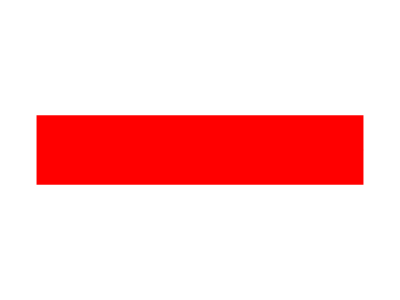
| From Around | At Address | In |  | From Around | At Address | In
Visited the Red Pirate Shop for 1/2 hr |  | Ha-Melakha St 13 | Or Yehuda | -Graphics- |  | Ha-Melakha St 13 | Or Yehuda
Work at Avigdor Warsaw School | Wed 26 Feb 2020 07:30:00 | Nakhal Gamla St 10 | Qiryat Ono | -Graphics- | Wed 26 Feb 2020 13:00:00 | Nakhal Gamla St 10 | Qiryat Ono
Sports hall near Ganei Tikva Municipal Library | Wed 26 Feb 2020 17:15:00 | Derech HaYam 9 | Ganne Tiqwa | -Graphics- | Wed 26 Feb 2020 18:00:00 | Derech HaYam 9 | Ganne Tiqwa
Wedding at Harmonia BaGan at Gedera Junction | Wed 26 Feb 2020 19:30:00 | HaAdom 28 | Gedera | -Graphics- | Wed 26 Feb 2020 22:30:00 | HaAdom 28 | Gedera
Qiryat Ono Mall, TOGO shoes , Renoir Women (Top Floor), Fox Women (Entrance), Fox Kids (Entrance) and Shufersal | Thu 27 Feb 2020 18:00:00 | Shlomo ha-Melekh St 37 | Qiryat Ono | -Graphics- | Thu 27 Feb 2020 20:30:00 | Shlomo ha-Melekh St 37 | Qiryat Ono
Bus 55 | Thu 27 Feb 2020 20:30:00 | Shlomo ha-Melekh St 37 | Qiryat Ono | -Graphics- | Thu 27 Feb 2020 20:45:00 | Hari Yehuda | Ganne Tiqwa
Work at Avigdor Warsaw School | Fri 28 Feb 2020 07:30:00 | Nakhal Gamla St 10 | Qiryat Ono | -Graphics- | Fri 28 Feb 2020 12:00:00 | Nakhal Gamla St 10 | Qiryat Ono
Home quarantine | Fri 28 Feb 2020 12:00:00 |  | Ganne Tiqwa | -Graphics- |  |  | Ganne Tiqwa

```mathematica
MakePrintableTable[14]
```

## Making Maps

### Javascript Maps

```mathematica
CreateBubbleTexts[key_]:=((Table[{"'<strong>"<>#["Detail"]<>"</strong><p>"<>If[DateObjectQ[#["StartTime"]],DateString[#["StartTime"]],""]<>"-"<>If[DateObjectQ[#["EndTime"]],DateString[#["EndTime"]],""]<>"</p><p>"<>#["StartLocation"]["Address"]<>" - "<>#["EndLocation"]["Address"]<>"</p><p>"<>If[StringQ[#["StartLocation"]["Object"]],#["StartLocation"]["Object"],#["StartLocation"]["Object"]["Name"]]<>" - "<>If[StringQ[#["EndLocation"]["Object"]],#["EndLocation"]["Object"],#["EndLocation"]["Object"]["Name"]]<>"</p>'",t},{t,GetCoordinates[#]}]&)/@DataWithKey[key]["Actions"])//Flatten[#,1]&;
```

```mathematica
GetMunicipalityCoordinate[key_]:={"'<strong>"<>DataWithKey[key]["Nickname"]<>"</strong><p>"<>If[StringQ[DataWithKey[key]["Address"]["Object"]],DataWithKey[key]["Address"]["Object"],DataWithKey[key]["Address"]["Object"]["Name"]]<>"</p>'",If[DataWithKey[key]["Address"]["Coordinate"]=={},DataWithKey[key]["Address"]["Object"]["Coordinates"],DataWithKey[key]["Address"]["Coordinate"]]}
```

```mathematica
GetCoordinates[action_]:=Module[{startcoord,endcoord,startobjcoord,endobjcoord},
startcoord=action["StartLocation"]["Coordinate"]//If[Length[#]==0,{},#]&;
endcoord=action["EndLocation"]["Coordinate"]//If[Length[#]==0,{},#]&;
startobjcoord=If[StringQ[action["StartLocation"]["Object"]],{},If[action["StartLocation"]["Object"]["Name"]=="Ben Gurion International Airport", Entity["Airport","LLBG"]["Coordinates"],{}]];
endobjcoord=If[StringQ[action["EndLocation"]["Object"]],{},If[action["EndLocation"]["Object"]["Name"]=="Ben Gurion International Airport", Entity["Airport","LLBG"]["Coordinates"],{}]];
{startcoord,endcoord,startobjcoord,endobjcoord}//DeleteDuplicates//DeleteCases[#,{}]&//DeleteCases[#,Null]&
];
```

```mathematica
GenerateFeatures[key_]:=StringJoin["{
                        'type': 'Feature',
                        'properties': {
                            'description':
                                ",GetMunicipalityCoordinate[key]⟦1⟧,",
                            'icon': 'marker'
                        },
                        'geometry': {
                            'type': 'Point',
                            'coordinates': [",ToString[GetMunicipalityCoordinate[key]⟦2,2⟧],", ",ToString[GetMunicipalityCoordinate[key]⟦2,1⟧],"]
                        }
                    },\n"]<>StringJoin["{
                        'type': 'Feature',
                        'properties': {
                            'description':
                                "<>#⟦1⟧<>",
                            'icon': 'information'
                        },
                        'geometry': {
                            'type': 'Point',
                            'coordinates': ["<>ToString[#⟦2,2⟧]<>", "<>ToString[#⟦2,1⟧]<>"]
                        }
                    },\n"&/@CreateBubbleTexts[key]];
```

```mathematica
FileHead[key_]:="<!DOCTYPE html>
<html>
<head>
<meta charset=\"utf-8\" />
<title>Display a popup on click</title>
<meta name=\"viewport\" content=\"initial-scale=1,maximum-scale=1,user-scalable=no\" />
<script src=\"https://api.mapbox.com/mapbox-gl-js/v1.8.1/mapbox-gl.js\"></script>
<link href=\"https://api.mapbox.com/mapbox-gl-js/v1.8.1/mapbox-gl.css\" rel=\"stylesheet\" />
<style>
\tbody { margin: 0; padding: 0; }
\t#map { position: absolute; top: 0; bottom: 0; width: 100%; }
</style>
</head>
<body>
<style>
    .mapboxgl-popup {
        max-width: 400px;
        font: 12px/20px 'Helvetica Neue', Arial, Helvetica, sans-serif;
    }
</style>
<div id=\"map\"></div>
<script>
\tmapboxgl.accessToken = 'pk.eyJ1IjoidHlvdGFrdWtpIiwiYSI6ImNrN2o0anFoazAybWgzbm83MnRsaW93aGgifQ.RUlPKLHV5_2JXPPVr8gLgw';
    var map = new mapboxgl.Map({
        container: 'map',
        style: 'mapbox://styles/mapbox/streets-v11',
        center: ["<>ToString[(Join[CreateBubbleTexts[key]⟦All,2⟧,{GetMunicipalityCoordinate[key]⟦2⟧}]//Mean)⟦2⟧]<>", "<>ToString[(Join[CreateBubbleTexts[key]⟦All,2⟧,{GetMunicipalityCoordinate[key]⟦2⟧}]//Mean)⟦1⟧]<>"],
        zoom: 6
    });
    
    map.on('load', function() {
        map.addSource('places', {
            'type': 'geojson',
            'data': {
                'type': 'FeatureCollection',
                'features': [\n";
FileEnd[key_]:="                ]
            }
        });
        // Add a layer showing the places.
        map.addLayer({
            'id': 'places',
            'type': 'symbol',
            'source': 'places',
            'layout': {
                'icon-image': '{icon}-15',
                'icon-allow-overlap': true,
                'icon-size': 5
            }
        });

        // When a click event occurs on a feature in the places layer, open a popup at the
        // location of the feature, with description HTML from its properties.
        map.on('click', 'places', function(e) {
            var coordinates = e.features[0].geometry.coordinates.slice();
            var description = e.features[0].properties.description;

            // Ensure that if the map is zoomed out such that multiple
            // copies of the feature are visible, the popup appears
            // over the copy being pointed to.
            while (Math.abs(e.lngLat.lng - coordinates[0]) > 180) {
                coordinates[0] += e.lngLat.lng > coordinates[0] ? 360 : -360;
            }

            new mapboxgl.Popup()
                .setLngLat(coordinates)
                .setHTML(description)
                .addTo(map);
        });

        // Change the cursor to a pointer when the mouse is over the places layer.
        map.on('mouseenter', 'places', function() {
            map.getCanvas().style.cursor = 'pointer';
        });

        // Change it back to a pointer when it leaves.
        map.on('mouseleave', 'places', function() {
            map.getCanvas().style.cursor = '';
        });
    });
</script>

</body>
</html>";
```

```mathematica
Table[Export["maps/map"<>If[NumberQ[key],ToString[key],key]<>".html",StringDrop[FileHead[key]<>GenerateFeatures[key],-2]<>"\n"<>FileEnd[key],"Text"],{key,ListOfPatients}];
```

StringJoin::string: String expected at position 2 in '<strong>Shaarei HaShamayim Synagogue 2nd Floor</strong><p>Thu 5 Mar 2020 06:00:00-Thu 5 Mar 2020 07:00:00</p><p><>Null[Address]<> - <>Null[Address]<></p><p><>Null[Object][Name]<> - <>Null[Object][Name]<></p>'.

StringJoin::string: String expected at position 4 in '<strong>Shaarei HaShamayim Synagogue 2nd Floor</strong><p>Thu 5 Mar 2020 06:00:00-Thu 5 Mar 2020 07:00:00</p><p><>Null[Address]<> - <>Null[Address]<></p><p><>Null[Object][Name]<> - <>Null[Object][Name]<></p>'.

StringJoin::string: String expected at position 6 in '<strong>Shaarei HaShamayim Synagogue 2nd Floor</strong><p>Thu 5 Mar 2020 06:00:00-Thu 5 Mar 2020 07:00:00</p><p><>Null[Address]<> - <>Null[Address]<></p><p><>Null[Object][Name]<> - <>Null[Object][Name]<></p>'.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Mean::rectt: Rectangular array expected at position 1 in Mean[{{31.7622,35.2142},{31.7554,35.214},{31.7535,35.2138},{31.7528,35.2164},{31.7622,35.2142},{31.7622,35.2142},Null[Coordinate],If[Null[Object][Name]==Ben Gurion International Airport,Ben Gurion International Airport[Coordinates],{}],Null[Coordinate],If[Null[Object][Name]==Ben Gurion International Airport,Ben Gurion International Airport[Coordinates],{}],{31.7535,35.2138},{31.7628,35.2183},{31.7622,35.2142},{31.7622,35.2142},{32.0528,34.778},{31.78,35.22}}].

Part::partw: Part 2 of Mean[{{31.7622,35.2142},{31.7554,35.214},{31.7535,35.2138},{31.7528,35.2164},{31.7622,35.2142},{31.7622,35.2142},Null[Coordinate],If[Null[Object][Name]==Ben Gurion International Airport,Ben Gurion International Airport[Coordinates],{}],Null[Coordinate],If[Null[Object][Name]==Ben Gurion International Airport,Ben Gurion International Airport[Coordinates],{}],{31.7535,35.2138},{31.7628,35.2183},{31.7622,35.2142},{31.7622,35.2142},{32.0528,34.778},{31.78,35.22}}] does not exist.

Mean::rectt: Rectangular array expected at position 1 in Mean[{{31.7622,35.2142},{31.7554,35.214},{31.7535,35.2138},{31.7528,35.2164},{31.7622,35.2142},{31.7622,35.2142},Null[Coordinate],If[Null[Object][Name]==Ben Gurion International Airport,Ben Gurion International Airport[Coordinates],{}],Null[Coordinate],If[Null[Object][Name]==Ben Gurion International Airport,Ben Gurion International Airport[Coordinates],{}],{31.7535,35.2138},{31.7628,35.2183},{31.7622,35.2142},{31.7622,35.2142},{32.0528,34.778},{31.78,35.22}}].

Part::partw: Part 2 of Null[Coordinate] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[«1»,-2].

Mean::rectt: Rectangular array expected at position 1 in Mean[{{32.0114,34.8867},{32.0114,34.8867},WestBank[Coordinates]}].

General::stop: Further output of Mean::rectt will be suppressed during this calculation.

### Generic Map for Israel and Municipalities

```mathematica
Municipalities[key_]:=Select[{#["StartLocation"]["Object"],#["EndLocation"]["Object"]}&/@DataWithKey[key]["Actions"]//Flatten//DeleteDuplicates,(Head[#]==Entity)&];
LocationCoordinates[key_]:=GeoPosition/@Select[{#["StartLocation"]["Coordinate"],#["EndLocation"]["Coordinate"]}&/@DataWithKey[key]["Actions"]//Flatten[#,1]&//DeleteDuplicates,#≠""∨#≠{}&];
AddressMunicipality[key_]:=DataWithKey[key]["Address"]["Object"]//(If[Head[#]==Entity,#])&;
AddressCoordinate[key_]:=(DataWithKey[key]["Address"]["Coordinate"]//(If[Length[#]≠0,#])&)//If[ListQ[#],GeoPosition[#]]&;
```

```mathematica
MapOfIsrael={GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]]};
```

```mathematica
GetRegion[entity_]:=(If[MissingQ[entity["AdministrativeDivision"]],If[MissingQ[entity["Cities"]],entity,entity["Cities"]⟦1⟧["AdministrativeDivision"]],entity["AdministrativeDivision"]])//If[#["Country"]["Name"]=="West Bank",Entity["Country","WestBank"],#]&;
GetRegionOutline[entity_]:={GeoStyling[Black],Polygon[GetRegion[entity]]};
```

```mathematica
AddressMunicipalityOutline[key_]:={GeoStyling[Black],Polygon[GetRegion[AddressMunicipality[key]]]};
```

```mathematica
ShowOutlineMap[key_]:=GeoGraphics[{MapOfIsrael,GetRegionOutline/@Municipalities[key],AddressMunicipalityOutline[key],GeoMarker[#,Entity["Icon","FirstAid"],"Color"->Red]&/@Municipalities[key],(GeoMarker[#,Entity["Icon","FirstAid"],"Color"->Red]&/@LocationCoordinates[key]),(GeoMarker[AddressMunicipality[key],Entity["Icon","Building"],"Color"->Blue])},ImageSize->Large,GeoBackground->None,GeoRangePadding->{Quantity[10,"Kilometers"],Quantity[300,"Kilometers"]}]
```

```mathematica
ShowDetailedMap[key_]:=GeoGraphics[{GeoMarker[#,Entity["Icon","FirstAid"],"Color"->Red]&/@DeleteCases[Municipalities[key],Entity["Airport","LLBG"]],(GeoMarker[#,Entity["Icon","FirstAid"],"Color"->Red]&/@LocationCoordinates[key]),(GeoMarker[AddressMunicipality[key],Entity["Icon","Building"],"Color"->Blue])},ImageSize->Large]
```

```mathematica
DeleteCases[Municipalities[5],Entity["Airport","LLBG"]]
```

{}

```mathematica
Entity["Airport","LLBG"]//Length
```

2

```mathematica
Entity["Airport","LLBG"]["Name"]
```

Ben Gurion International Airport

## Making Country List and Contact List

```mathematica
CountryWithMultiplicity=Reverse/@Module[{listofcountries,deletedup},
listofcountries=Table[DataWithKey[key]["SourceCountry"],{key,ListOfPatients}];
deletedup=DeleteDuplicates[listofcountries];
{#,Count[listofcountries,#]}&/@deletedup]
```

{{13,Italy},{24,Israel},{1,Japan},{2,United States},{1,Greece},{1,West Bank},{16,Spain},{4,Switzerland},{12,Austria},{4,France},{1,Belgium},{1,India},{1,Azerbaijan},{3,Germany},{1,Czech Republic},{1,Entity[Country,]},{1,United Kingdom}}

```mathematica
Export["images/sourcecountries.jpeg",GeoListPlot[CountryWithMultiplicity[[All,2]],ImageSize->500],"JPEG",ImageResolution->200]
```

images/sourcecountries.jpeg

```mathematica
ContactList=Table[DataWithKey[key]["RelatedPerson"]->key,{key,ListOfPatients}];
```

```mathematica
LayeredGraphPlot[ContactList,PlotTheme->"DiagramGreen",AspectRatio->0.5,VertexSize->0.6,VertexLabelStyle->6,ImageSize->1000]
```

-Graphics-

```mathematica
Export["images/transmissiondiagram.svg",LayeredGraphPlot[ContactList,PlotTheme->"DiagramGreen",AspectRatio->0.5,VertexSize->0.6,VertexLabelStyle->6,ImageSize->1000],"SVG"]
```

images/transmissiondiagram.svg

## Making Final Map

```mathematica
ExportImages[key_]:=Module[{filename1,filename2,mystring},
filename1="images/outlinemap"<>If[NumberQ[key],ToString[key],key]<>".svg";
filename2="images/detailedmap"<>If[NumberQ[key],ToString[key],key]<>".jpeg";
Export[filename1,ShowOutlineMap[key],"SVG"];
Export[filename2,ShowDetailedMap[key],"JPEG",ImageResolution->300];
mystring="<h3"<>" id=\""<>If[NumberQ[key],ToString[key],key]<>"\">"<>"Patient Number "<>ToString[DataWithKey[key]["Key"]]<>" "<>DataWithKey[key]["Nickname"]<>" at "<>ToString[DataWithKey[key]["Address"]["Object"]["Name"]]<>" <a href=\"#thetop\"  class=\"small button icon fa-level-up\">To Top</a><a href=\""<>"maps/map"<>If[NumberQ[key],ToString[key],key]<>".html"<>"\"  class=\"small button icon fa-map-o\" target=\"_blank\">Interactive Map</a></h3>\n"<>"<div class=\"posts\">\n\t<article>\n\t\t<a href=\""<>filename1<>"\" class=\"image\"><img src=\""<>filename1<>"\" alt=\"\" height=300 /></a>\n\t\t<h4>Outlined Map</h4>\n\t</article>\n\t<article>\n\t\t<a href=\""<>filename2<>"\" class=\"image\"><img src=\""<>filename2<>"\" alt=\"\" height=300/></a>\n\t\t<h4>Detailed Map</h4>\n\t</article>\n</div>\n<div>"<>MakeHTMLTable[key]<>"\n</div>\n<hr class=\"major\" />\n";
mystring
];
ExportImagesWritePageOnly[key_]:=Module[{filename1,filename2,mystring},
filename1="images/outlinemap"<>If[NumberQ[key],ToString[key],key]<>".svg";
filename2="images/detailedmap"<>If[NumberQ[key],ToString[key],key]<>".jpeg";
mystring="<h3"<>" id=\""<>If[NumberQ[key],ToString[key],key]<>"\">"<>"Patient Number "<>ToString[DataWithKey[key]["Key"]]<>" "<>DataWithKey[key]["Nickname"]<>" at "<>ToString[DataWithKey[key]["Address"]["Object"]["Name"]]<>" <a href=\"#thetop\"  class=\"small button icon fa-level-up\">To Top</a><a href=\""<>"maps/map"<>If[NumberQ[key],ToString[key],key]<>".html"<>"\"  class=\"small button icon fa-map-o\" target=\"_blank\">Interactive Map</a></h3>\n"<>"<div class=\"posts\">\n\t<article>\n\t\t<a href=\""<>filename1<>"\" class=\"image\"><img src=\""<>filename1<>"\" alt=\"\" height=300 /></a>\n\t\t<h4>Outlined Map</h4>\n\t</article>\n\t<article>\n\t\t<a href=\""<>filename2<>"\" class=\"image\"><img src=\""<>filename2<>"\" alt=\"\" height=300/></a>\n\t\t<h4>Detailed Map</h4>\n\t</article>\n</div>\n<div>"<>MakeHTMLTable[key]<>"\n</div>\n<hr class=\"major\" />\n";
mystring
];
HeadHTML="<!DOCTYPE HTML>
<!--
\tEditorial by HTML5 UP
\thtml5up.net | @ajlkn
\tFree for personal and commercial use under the CCA 3.0 license (html5up.net/license)
-->
<html>
\t<head>
\t\t<title>2019-2020 Israel, West Bank and Gaza Coronavirus Outbreak</title>
\t\t<meta charset=\"utf-8\" />
\t\t<meta name=\"viewport\" content=\"width=device-width, initial-scale=1, user-scalable=no\" />
\t\t<!--[if lte IE 8]><script src=\"assets/js/ie/html5shiv.js\"></script><![endif]-->
\t\t<link rel=\"stylesheet\" href=\"assets/css/main.css\" />
\t\t<!--[if lte IE 9]><link rel=\"stylesheet\" href=\"assets/css/ie9.css\" /><![endif]-->
\t\t<!--[if lte IE 8]><link rel=\"stylesheet\" href=\"assets/css/ie8.css\" /><![endif]-->
\t</head>
\t<body>

\t\t<!-- Wrapper -->
\t\t\t<div id=\"wrapper\">

\t\t\t\t<!-- Main -->
\t\t\t\t\t<div id=\"main\">
\t\t\t\t\t\t<div class=\"inner\">

\t\t\t\t\t\t\t<!-- Header -->
\t\t\t\t\t\t\t\t<header id=\"header\">
\t\t\t\t\t\t\t\t\t<a href=\"index.html\" class=\"logo\"><strong>Editorial</strong> by HTML5 UP</a>
\t\t\t\t\t\t\t\t</header>

\t\t\t\t\t\t\t<!-- Content -->
\t\t\t\t\t\t\t\t<section>
\t\t\t\t\t\t\t\t\t<header class=\"main\">
\t\t\t\t\t\t\t\t\t\t<h1 id=\"thetop\">2019-2020 Israel, West Bank and Gaza Coronavirus Outbreak</h1>
\t\t\t\t\t\t\t\t\t</header>
\t\t\t\t\t\t\t\t\t<span class=\"image main\"><img src=\"images/totalcases.svg\" alt=\"\" /></span>
                                    <div class=\"posts\">
                                        <article>
                                            <a href=\"images/sourcecountries.jpeg\" class=\"image\"><img src=\"images/sourcecountries.jpeg\" alt=\"\" height=300 /></a>
                                            <h4>Source Countries</h4>
                                        </article>
                                        <article>
                                            <a href=\"images/transmissiondiagram.svg\" class=\"image\"><img src=\"images/transmissiondiagram.svg\" alt=\"\" height=300/></a>
                                            <h4>Exposure Diagram Between the Patients</h4>
                                        </article>
                                    </div>
\t\t\t\t\t\t\t\t\t<h3>Introduction</h3>
\t\t\t\t\t\t\t\t\t<p>The patient information and geographic data are based on the press release by the Israeli Ministry of Health from the two following websites: the Hebrew <a href=\"https://t.me/s/MOHreport\">telegraph page</a> and <a href=\"https://www.health.gov.il/Subjects/disease/corona/Pages/press-release.aspx?fbclid=IwAR3dAd_1nauO7hjBk5hjERF1DBnrKT5ac5-OLuyRENQc4iDpQX-KhrERYuE\">the Hebrew page of press releases</a>. Due to the rapid escalation of the pandemic, I have introduced a parser to collect these data automatically, the geographic data are still manually inputed and verified. Expect grammartical mistakes and errors.</p>
                                    <p></p>
\t\t\t\t\t\t\t\t\t<p>This page presents all the cases of coronavirus disease published by the Ministry of Health as of "<>DateString[Now]<>". Please click on the case number for the corresponding cases:</p>\n";
GenerateHREF="<hr class=\"major\" />\n"<>StringJoin@@Table["<a href=\"#"<>If[NumberQ[k],ToString[k],k]<>"\"  class=\"small button icon fa-level-down\">"<>If[NumberQ[k],ToString[k],k]<>"</a>\t",{k,ListOfPatients}]<>"\n<hr class=\"major\" />\n"
TailHTML="\n\t\t\t\t\t\t</section>
                        <section id=\"banner\">
\t\t\t\t\t\t\t\t\t<div class=\"content\">
\t\t\t\t\t\t\t\t\t\t<h3>Visitors to this map</h3>
\t\t\t\t\t\t\t\t\t\t<p>This map is created by Zhuohui Zhang <a href=\"mailto:zhuohui.zhang@gmail.com\">zhuohui.zhang@gmail.com</a> based on the information released by the Israeli Ministry of Health</p>
\t\t\t\t\t\t\t\t\t\t<ul class=\"actions\">
\t\t\t\t\t\t\t\t\t\t\t<li><a href=\"https://t.me/s/MOHreport\" class=\"button big\">Learn More</a></li>
\t\t\t\t\t\t\t\t\t\t</ul>
\t\t\t\t\t\t\t\t\t</div>
\t\t\t\t\t\t\t\t\t<span class=\"image object\">
\t\t\t\t\t\t\t\t\t\t<a href=\"https://m.maploco.com/details/7105yzdd\"><img style=\"border:0px;\" src=\"https://www.maploco.com/vmap/s/10030225.png\" alt=\"Locations of Site Visitors\" title=\"Locations of Site Visitors\"/></a>
\t\t\t\t\t\t\t\t\t</span>
                            <hr class=\"major\" />
\t\t\t\t        </section>
\t\t\t\t\t\t</div>
\t\t\t\t\t</div>

\
\t\t<!-- Scripts -->
\t\t\t<script src=\"assets/js/jquery.min.js\"></script>
\t\t\t<script src=\"assets/js/skel.min.js\"></script>
\t\t\t<script src=\"assets/js/util.js\"></script>
\t\t\t<!--[if lte IE 8]><script src=\"assets/js/ie/respond.min.js\"></script><![endif]-->
\t\t\t<script src=\"assets/js/main.js\"></script>

\t</body>
</html>";
```

<hr class="major" />
<a href="#3"  class="small button icon fa-level-down">3</a>	<a href="#4"  class="small button icon fa-level-down">4</a>	<a href="#5"  class="small button icon fa-level-down">5</a>	<a href="#6"  class="small button icon fa-level-down">6</a>	<a href="#7"  class="small button icon fa-level-down">7</a>	<a href="#8"  class="small button icon fa-level-down">8</a>	<a href="#9"  class="small button icon fa-level-down">9</a>	<a href="#10"  class="small button icon fa-level-down">10</a>	<a href="#11"  class="small button icon fa-level-down">11</a>	<a href="#12"  class="small button icon fa-level-down">12</a>	<a href="#13"  class="small button icon fa-level-down">13</a>	<a href="#14"  class="small button icon fa-level-down">14</a>	<a href="#15"  class="small button icon fa-level-down">15</a>	<a href="#A"  class="small button icon fa-level-down">A</a>	<a href="#B"  class="small button icon fa-level-down">B</a>	<a href="#C"  class="small button icon fa-level-down">C</a>	<a href="#16"  class="small button icon fa-level-down">16</a>	<a href="#17"  class="small button icon fa-level-down">17</a>	<a href="#18"  class="small button icon fa-level-down">18</a>	<a href="#19"  class="small button icon fa-level-down">19</a>	<a href="#20"  class="small button icon fa-level-down">20</a>	<a href="#21"  class="small button icon fa-level-down">21</a>	<a href="#D"  class="small button icon fa-level-down">D</a>	<a href="#E"  class="small button icon fa-level-down">E</a>	<a href="#22"  class="small button icon fa-level-down">22</a>	<a href="#23"  class="small button icon fa-level-down">23</a>	<a href="#24"  class="small button icon fa-level-down">24</a>	<a href="#25"  class="small button icon fa-level-down">25</a>	<a href="#26"  class="small button icon fa-level-down">26</a>	<a href="#27"  class="small button icon fa-level-down">27</a>	<a href="#28"  class="small button icon fa-level-down">28</a>	<a href="#29"  class="small button icon fa-level-down">29</a>	<a href="#30"  class="small button icon fa-level-down">30</a>	<a href="#31"  class="small button icon fa-level-down">31</a>	<a href="#32"  class="small button icon fa-level-down">32</a>	<a href="#33"  class="small button icon fa-level-down">33</a>	<a href="#34"  class="small button icon fa-level-down">34</a>	<a href="#35"  class="small button icon fa-level-down">35</a>	<a href="#36"  class="small button icon fa-level-down">36</a>	<a href="#37"  class="small button icon fa-level-down">37</a>	<a href="#38"  class="small button icon fa-level-down">38</a>	<a href="#39"  class="small button icon fa-level-down">39</a>	<a href="#F"  class="small button icon fa-level-down">F</a>	<a href="#40"  class="small button icon fa-level-down">40</a>	<a href="#41"  class="small button icon fa-level-down">41</a>	<a href="#42"  class="small button icon fa-level-down">42</a>	<a href="#43"  class="small button icon fa-level-down">43</a>	<a href="#44"  class="small button icon fa-level-down">44</a>	<a href="#45"  class="small button icon fa-level-down">45</a>	<a href="#46"  class="small button icon fa-level-down">46</a>	<a href="#47"  class="small button icon fa-level-down">47</a>	<a href="#48"  class="small button icon fa-level-down">48</a>	<a href="#49"  class="small button icon fa-level-down">49</a>	<a href="#50"  class="small button icon fa-level-down">50</a>	<a href="#G"  class="small button icon fa-level-down">G</a>	<a href="#51"  class="small button icon fa-level-down">51</a>	<a href="#52"  class="small button icon fa-level-down">52</a>	<a href="#53"  class="small button icon fa-level-down">53</a>	<a href="#54"  class="small button icon fa-level-down">54</a>	<a href="#55"  class="small button icon fa-level-down">55</a>	<a href="#56"  class="small button icon fa-level-down">56</a>	<a href="#57"  class="small button icon fa-level-down">57</a>	<a href="#58"  class="small button icon fa-level-down">58</a>	<a href="#59"  class="small button icon fa-level-down">59</a>	<a href="#60"  class="small button icon fa-level-down">60</a>	<a href="#61"  class="small button icon fa-level-down">61</a>	<a href="#62"  class="small button icon fa-level-down">62</a>	<a href="#63"  class="small button icon fa-level-down">63</a>	<a href="#64"  class="small button icon fa-level-down">64</a>	<a href="#65"  class="small button icon fa-level-down">65</a>	<a href="#66"  class="small button icon fa-level-down">66</a>	<a href="#67"  class="small button icon fa-level-down">67</a>	<a href="#68"  class="small button icon fa-level-down">68</a>	<a href="#69"  class="small button icon fa-level-down">69</a>	<a href="#70"  class="small button icon fa-level-down">70</a>	<a href="#71"  class="small button icon fa-level-down">71</a>	<a href="#72"  class="small button icon fa-level-down">72</a>	<a href="#73"  class="small button icon fa-level-down">73</a>	<a href="#74"  class="small button icon fa-level-down">74</a>	<a href="#75"  class="small button icon fa-level-down">75</a>	<a href="#76"  class="small button icon fa-level-down">76</a>	<a href="#77"  class="small button icon fa-level-down">77</a>	<a href="#78"  class="small button icon fa-level-down">78</a>	<a href="#79"  class="small button icon fa-level-down">79</a>	<a href="#80"  class="small button icon fa-level-down">80</a>	<a href="#81"  class="small button icon fa-level-down">81</a>	<a href="#82"  class="small button icon fa-level-down">82</a>	
<hr class="major" />

```mathematica
Export["images/frontpage.jpeg",GeoListPlot[{Entity["Country","China"],Entity["Country","SouthKorea"],Entity["Country","Italy"],Entity["Country","France"],Entity["Country","Switzerland"],Entity["Country","Spain"],Entity["Country","Andorra"],Entity["Country","SanMarino"],Entity["Country","Austria"],Entity["Country","Japan"],Entity["Country","Singapore"],Entity["Country","Thailand"],Entity["Country","Germany"]},ImageSize->500],"JPEG"];
```

```mathematica
Monitor[Export["index1.html",HeadHTML<>GenerateHREF<>StringJoin@@Table[ExportImages[key],{key,Reverse[ListOfPatients]}]<>TailHTML,"Text"],key]
```

GeoMarker::invpts: If[String==Entity,WestBank] is not a valid GeoMarker coordinates specification.

GeoGraphics::polpos: Unable to obtain polygon information for Geva Binyamin. Proceeding with average position GeoPosition[{31.85,35.2738}].

GeoGraphics::polpos: Unable to obtain polygon information for Maale Adummim. Proceeding with average position GeoPosition[{31.82,35.35}].

$Aborted

```mathematica
Monitor[Export["index1.html",HeadHTML<>GenerateHREF<>StringJoin@@Table[ExportImagesWritePageOnly[key],{key,Reverse[ListOfPatients]}]<>TailHTML,"Text"],key]
```

index1.html

# Collapse

```mathematica
ListOfPatients[[1;;4]]
```

{3,4,5,6}

```mathematica
Export["redarrow.gif",Graphics[{Red,Thickness[0.05],Arrowheads[0.01],Arrow[{{0,0},{0.2,0}}]},PlotRange->{{-0.01,0},{0.2,0.01}}],"GIF"]
```

redarrow.gif

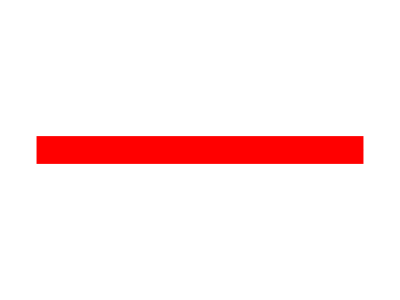

```mathematica
Graphics[{Red,Thickness[0.05],Arrowheads[0.01],Arrow[{{0,0},{0.2,0}}]},PlotRange->Automatic]
```

```mathematica
GridShowMap[key_]:=Grid[{{ShowOutlineMap[key],ShowDetailedMap[key]}},ItemSize->{{Scaled[0.2], Scaled[0.2]}}];
GridShowTableAndMap[key_]:=Grid[{{Text[Style["Patient Number "<>ToString[DataWithKey[key]["Key"]]<>" "<>DataWithKey[key]["Nickname"]<>" at "<>ToString[DataWithKey[key]["Address"]["Object"]["Name"]],Large,Black,FontFamily->"Times New Roman"]]},{GridShowMap[key]},{MakePrintableTable[key]}}]
```

```mathematica
??Cell
```

```mathematica
With[{key=3},Cell["Patient Number "<>ToString[DataWithKey[key]["Key"]]<>" "<>DataWithKey[key]["Nickname"]<>" at "<>ToString[DataWithKey[key]["Address"]["Object"]["Name"]],"Section"]]
```

Cell[Patient Number 3 The Or Yehuda Shop Owner at Or Yehuda,Section]

```mathematica
GridShowTableAndMap[6]
```

Patient Number 6 Imported from Italy No1 at Haifa
-Graphics-
 | From Around | At Address | In |  | From Around | At Address | In
Flight AZ810 from Italy |  |  |  | -Graphics- | Sun 23 Feb 2020 03:00:00 | Ben Gurion Airport | Ben Gurion International Airport
Aroma at Paz gas station near Pancake House | Sat 22 Feb 2020 06:30:00 | Kvish HaHof | Beit Jann | -Graphics- | Sat 22 Feb 2020 07:00:00 | Kvish HaHof | Beit Jann
Said Malham Electric Appliances | Sat 22 Feb 2020 11:00:00 |  | Abu Snan | -Graphics- | Sat 22 Feb 2020 13:00:00 |  | Abu Snan
Sportswear Store Mechsenei Zol Sport | Sat 22 Feb 2020 11:00:00 | Yehuda Itin St 5 | Haifa | -Graphics- | Sat 22 Feb 2020 13:00:00 | Yehuda Itin St 5 | Haifa
Parliament Hummus at Paz gas station | Sun 23 Feb 2020 11:30:00 | Kvish 4 | Nahariyya | -Graphics- | Sun 23 Feb 2020 12:00:00 | Kvish 4 | Nahariyya

```mathematica
Print[GridShowTableAndMap[3]]
NotebookWrite[ayr9p_shm117FrontEndObject[LinkObject["ayr9p_shm", 3, 1]]117"AutomatedImport.nb""/Users/zhuohuizhang/Dropbox/IsraelCases/AutomatedImport.nb",Cell["Patient Number "<>ToString[DataWithKey[3]["Key"]]<>" "<>DataWithKey[3]["Nickname"]<>" at "<>ToString[DataWithKey[3]["Address"]["Object"]["Name"]],"Section"],"All"];
```

Patient Number 3 The Or Yehuda Shop Owner at Or Yehuda
-Graphics-
 | From Around | At Address | In |  | From Around | At Address | In
El Al flight LY382 |  |  |  | -Graphics- | Sun 23 Feb 2020 16:10:00 | Ben Gurion Airport | Ben Gurion International Airport
The Red Pirate Store | Sun 23 Feb 2020 18:00:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Sun 23 Feb 2020 22:00:00 | Ha-Melakha St 13 | Or Yehuda
The Red Pirate Store | Mon 24 Feb 2020 08:30:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Tue 25 Feb 2020 00:00:00 | Ha-Melakha St 13 | Or Yehuda
The Red Pirate Store | Tue 25 Feb 2020 08:30:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Wed 26 Feb 2020 00:00:00 | Ha-Melakha St 13 | Or Yehuda
The Red Pirate Store | Wed 26 Feb 2020 16:00:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Wed 26 Feb 2020 21:00:00 | Ha-Melakha St 13 | Or Yehuda
Irus Synagogue in Irus | Mon 24 Feb 2020 06:00:00 | Noga Street | Irus | -Graphics- | Mon 24 Feb 2020 07:00:00 | Noga Street | Irus

Patient Number 3 The Or Yehuda Shop Owner at Or Yehuda
-Graphics-
 | From Around | At Address | In |  | From Around | At Address | In
El Al flight LY382 |  |  |  | -Graphics- | Sun 23 Feb 2020 16:10:00 | Ben Gurion Airport | Ben Gurion International Airport
The Red Pirate Store | Sun 23 Feb 2020 18:00:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Sun 23 Feb 2020 22:00:00 | Ha-Melakha St 13 | Or Yehuda
The Red Pirate Store | Mon 24 Feb 2020 08:30:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Tue 25 Feb 2020 00:00:00 | Ha-Melakha St 13 | Or Yehuda
The Red Pirate Store | Tue 25 Feb 2020 08:30:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Wed 26 Feb 2020 00:00:00 | Ha-Melakha St 13 | Or Yehuda
The Red Pirate Store | Wed 26 Feb 2020 16:00:00 | Ha-Melakha St 13 | Or Yehuda | -Graphics- | Wed 26 Feb 2020 21:00:00 | Ha-Melakha St 13 | Or Yehuda
Irus Synagogue in Irus | Mon 24 Feb 2020 06:00:00 | Noga Street | Irus | -Graphics- | Mon 24 Feb 2020 07:00:00 | Noga Street | Irus